# Monetary Policy

## Setup

Set working directory

```mathematica
SetDirectory["/Users/nicoloceneda/Dropbox/Bhamra-Ceneda/theory/macroeconomics/code"];
```

## Consumption and Investment

## Maximum Safe to Spend

Maximum safe to spend

```mathematica
maxC[μ_,T_]:=(μ *w0)/((1+μ)-(1+μ)^(1-T))
```

Maximum safe to spend when μ = 0

```mathematica
Limit[(w0*μ)/((1+μ)-(1+μ)^(1-T)),μ->0]
```

w0/T

Household wealth

```mathematica
w[μ_,t_,T_]:=w0*(1+μ)^t-maxC[μ,T]*(1+μ)*((1+μ)^t-1)/μ
```

Parameters

```mathematica
w0=1;
```

Plot household maximum safe to spend and wealth

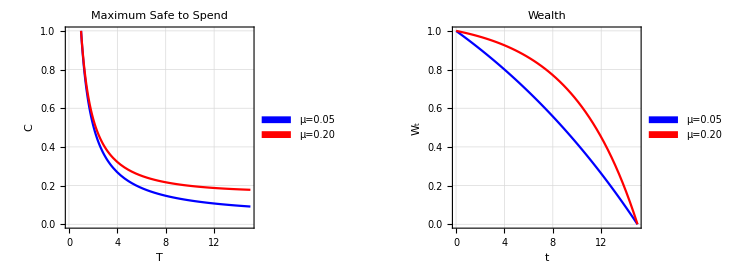

```mathematica
householdConsumption= Plot[{maxC[0.05,T],maxC[0.20,T]},{T,0.01,15},
PlotStyle->{Blue,Red},
PlotLabel->"Maximum Safe to Spend",
PlotLegends->Placed[SwatchLegend[{"μ=0.05","μ=0.20"}],{0.87,0.88}],
FrameLabel->{"T","C"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,15},{0,1}}];
householdWealth= Plot[{w[0.05,t,15],w[0.20,t,15]},{t,0.01,15},
PlotStyle->{Blue,Red},
PlotLabel->"Wealth",
PlotLegends->Placed[SwatchLegend[{"μ=0.05","μ=0.20"}],{0.87,0.88}],
FrameLabel->{"t","W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,15},{0,1}}];
householdWealth=GraphicsGrid[{{householdConsumption,householdWealth}},ImageSize->{750,270}]
Export["images/household-wealth.jpeg",householdWealth];
```

## Optimal Consumption-Savings

Household utility

```mathematica
u[c_,η_]:=(c^(1-η)-1)/(1-η)
```

Plot household utility

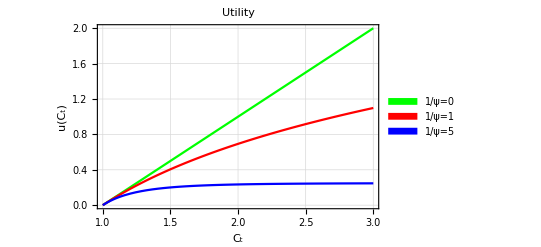

```mathematica
householdUtility=Plot[{u[c,0],Log[c],u[c,5]},{c,1,3},
PlotStyle->{Green,Red,Blue},
PlotLabel->"Utility",
PlotLegends->Placed[SwatchLegend[{"1/ψ=0","1/ψ=1","1/ψ=5"}],{0.12,0.75}],
FrameLabel->{"C_t","u(C_t)"},
Frame->True,
GridLines->Automatic,
PlotRange->{{1,3},{0,2}}]
Export["images/household-utility.jpeg",householdUtility];
```

Clear variables

```mathematica
Clear["Global`*"]
```

Optimal consumption-wealth ratio

```mathematica
optimalCW[β_,ψ_,μ_]:=(1+μ)^(1-ψ)/((1+μ)^(1-ψ)+β^ψ)
```

Plot optimal savings-wealth ratio and consumption-wealth ratio

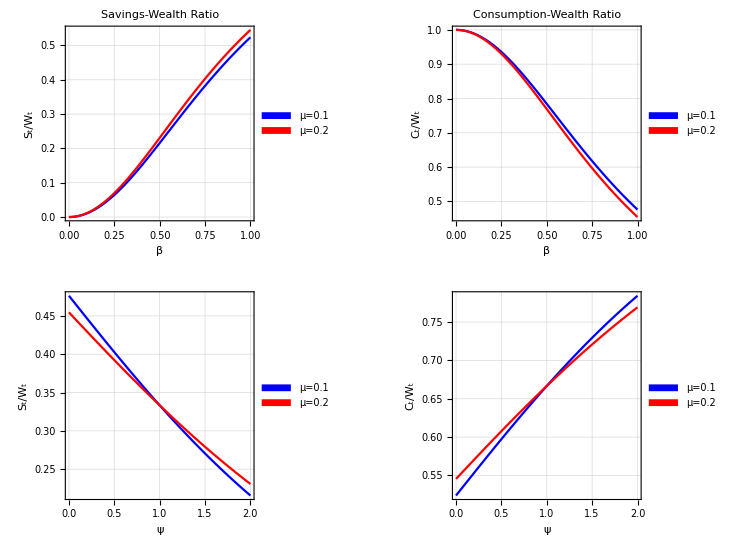

```mathematica
consumptionWealthBeta=Plot[{optimalCW[β,2,0.1],optimalCW[β,2,0.2]},{β,0,1},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Wealth Ratio",
PlotLegends->Placed[SwatchLegend[{"μ=0.1","μ=0.2"}],{0.87,0.88}],
FrameLabel->{"β","C_t/W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->All];
consumptionWealthPsi=Plot[{optimalCW[0.5,ψ,0.1],optimalCW[0.5,ψ,0.2]},{ψ,0,2},
PlotStyle->{Blue,Red},
PlotLegends->Placed[SwatchLegend[{"μ=0.1","μ=0.2"}],{0.12,0.88}],
FrameLabel->{"ψ","C_t/W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->All];
WealthRatios=GraphicsGrid[{{savingsWealthBeta,consumptionWealthBeta},
{savingsWealthPsi,consumptionWealthPsi}},ImageSize->{750,540}]
Export["images/wealth-ratios.jpeg",WealthRatios];
```

## Pontryagin' s maximum principle

Functionals

```mathematica
yCoordinate[x_]:=√(1-x^2)
vector=Graphics3D[{Red,Arrow[{{0.7,-yCoordinate[0.7],0},{0,0,0}}]},Axes->True,Boxed->True];
sphere=SphericalPlot3D[1,{θ,0,π/2},{ϕ,0,2 π},
ImageSize->Medium,
PlotStyle->{Directive[Blue,Specularity[White,1]],Opacity[0.4]}];
vectorSphere=Show[vector,sphere,AxesLabel->{"x","y","z"}]
Export["images/sphere.jpeg",vectorSphere];
```

-Graphics3D-